拟合函数: f = 604.976-196.031 x+476.39 x^2+205.192 x^3-1036.97 x^4

最小值位置: x/L = 0.221

最小共振频率: f = 584.662 Hz

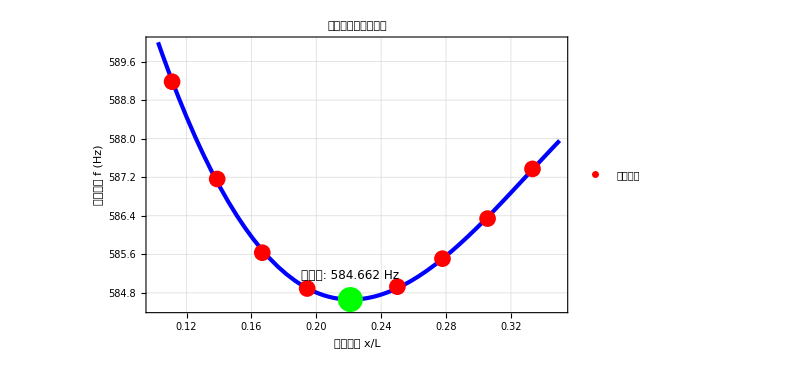

拟合优度 R.b2 = 0.9994

拟合优度 R.b2 = 1.

最小频率: f = -8.07469×10^419 Hz

合理的最小值: x/L = 1.654×10^104

拟合函数: f = 604.894-194.336 x+463.954 x^2+243.71 x^3-1079.76 x^4

FindMinimum::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

最小值位置: x/L = 1.65367×10^104

最小共振频率: f = -7.75468×10^419 Hz

-Graphics-

拟合优度 R.b2 = 1.

General::stop: 在本次计算中，StringJoin::string 的进一步输出将被抑制.

```mathematica
(*清除所有变量*)ClearAll["Global`*"]

(*输入数据*)
data={{0.1111,589.182},{0.1389,587.163},{0.1667,585.634},{0.1944,584.891},{0.2500,584.929},{0.2778,585.510},{0.3056,586.342},{0.3333,587.373}};

(*使用更稳定的方法-直接使用 Fit 而不是 NonlinearModelFit*)
fitFunction=Fit[data,{1,x,x^2,x^3,x^4},x];

Print["拟合函数: f = ",fitFunction];

(*使用更可靠的方法找到最小值*)
(*在数据范围内生成多个点来寻找最小值*)
testPoints=Table[{x,fitFunction},{x,0.1,0.35,0.001}];
minPoint=MinimalBy[testPoints,Last][[1]];

xMin=minPoint[[1]];
fMin=minPoint[[2]];

Print["最小值位置: x/L = ",NumberForm[xMin,4]];
Print["最小共振频率: f = ",NumberForm[fMin,6]," Hz"];

(*创建图形-确保正确的样式*)
plot=Plot[fitFunction,{x,0.1,0.35},PlotStyle->{Blue,Thickness[0.005]},PlotLabel->Style["黄铜棒共振频率拟合",16,Black,Bold],AxesLabel->{Style["悬挂位置 x/L",14,Black],Style["共振频率 f (Hz)",14,Black]},LabelStyle->{Black,12},AxesStyle->Black,Background->White,Frame->{{True,False},{True,False}},FrameStyle->Black,GridLines->Automatic,GridLinesStyle->LightGray,PlotRange->{{0.1,0.35},{584.5,590}},ImageSize->600];

(*组合所有图形元素*)
finalPlot=Show[plot,ListPlot[data,PlotStyle->{Red,PointSize[0.02]},PlotLegends->{"实验数据"}],Graphics[{Green,PointSize[0.03],Point[{xMin,fMin}],Black,Text[Style["最小值: "<>ToString[NumberForm[fMin,6]]<>" Hz",12,Background->White],{xMin,fMin+0.5},{0,-1.5}]}],PlotRange->{{0.1,0.35},{584.5,590}}];

(*显示最终结果*)
finalPlot

(*计算拟合优度*)
residuals=data[[All,2]]-(fitFunction/. x->#&/@data[[All,1]]);
ssRes=Total[residuals^2];
ssTot=Total[(data[[All,2]]-Mean[data[[All,2]]])^2];
rSquared=1-ssRes/ssTot;

Print["拟合优度 R.b2 = ",NumberForm[rSquared,4]];
```